```mathematica
ei1=vo==(vip-vin)GBW /(s+wo)
```

vo==(GBW (-vin+vip))/(s+wo)

```mathematica
ei2 = vin ->vo s/(s+wc)
```

vin→(s vo)/(s+wc)

```mathematica
ei3 = ei1/. ei2
```

vo==(GBW (vip-(s vo)/(s+wc)))/(s+wo)

```mathematica
ei4= Solve[ei3,vo][[1,1]]
```

vo→(GBW vip (s+wc))/(GBW s+s^2+s wc+s wo+wc wo)

```mathematica
ei4[[2,1]]
```

GBW

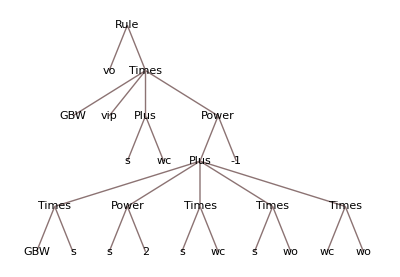

```mathematica
TreeForm[ei4]
```

```mathematica
e1 = InverseLaplaceTransform[(s+a)/(s^2+as+b),s,t]
```

(ⅇ^(-√(-as-b) t) (-a+√(-as-b)+a ⅇ^(2 √(-as-b) t)+√(-as-b) ⅇ^(2 √(-as-b) t)))/(2 √(-as-b))

```mathematica
e2 = Roots[s^2 + (wc+bw+w0)s +w0 wc==0,s]
```

s==1/2 (-bw-w0-wc-√(-4 w0 wc+(bw+w0+wc)^2))||s==1/2 (-bw-w0-wc+√(-4 w0 wc+(bw+w0+wc)^2))

```mathematica
e2[[1]]/.bw->2*Pi*3*10^6/.wc->10^6/.w0->18.9//N
```

s==-1.98496×10^7

```mathematica
e2[[2]]/.bw->2*Pi*3*10^6/.wc->10^6/.w0->18.9//N
```

s==-0.952161

```mathematica
(*Constant input initial condition: Vo=(s+a/(s^2+as+b)*vo(0)-b0)/(s^2+as+b)*vp(0)*)
```

```mathematica
ezi1=InverseLaplaceTransform[(s+(wc+bw+w0))/((s^2+(wc+bw+w0)s+w0 wc))/.bw->1*10^7/.wc->4*10^6/.w0->20//N,s,t]
```

-4.08163×10^-7 ⅇ^(-1.4×10^7 t)+1. ⅇ^(-5.71428 t)

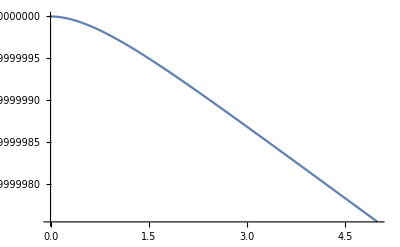

```mathematica
Plot[ezi1,{t,0,0.5*10^-6}]
```

```mathematica
ezi2=InverseLaplaceTransform[(-bw)/((s^2+(wc+bw+w0)s+w0 wc))/.bw->1*10^7/.wc->4*10^6/.w0->20//N,s,t]
```

-1.×10^7 (-7.14285×10^-8 ⅇ^(-1.4×10^7 t)+7.14285×10^-8 ⅇ^(-5.71428 t))

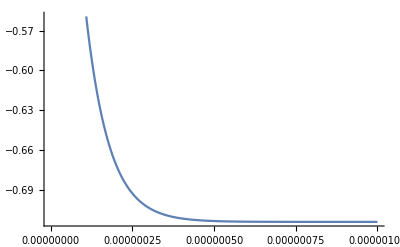

```mathematica
Plot[ezi2,{t,0,1*10^-6}]
```

```mathematica
ezi3=InverseLaplaceTransform[(s+(wc+bw+w0))/((s^2+(wc+bw+w0)s+w0 wc))-bw/((s^2+(wc+bw+w0)s+w0 wc))/.bw->1*10^7/.wc->4*10^6/.w0->20//N,s,t]
```

0.714285 ⅇ^(-1.4×10^7 t)+0.285715 ⅇ^(-5.71428 t)

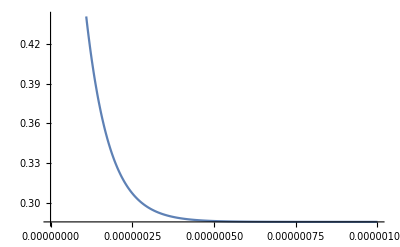

```mathematica
Plot[ezi3,{t,0,1*10^-6}]
```

```mathematica
(*Zero State Condition*)
```

```mathematica
ezs1=InverseLaplaceTransform[(bw s+bw wc)/(s(s^2+(wc+bw+w0)s+w0 wc))/.bw->1*10^7/.wc->4*10^6/.w0->20//N,s,t]
```

500000.-0.510204 ⅇ^(-1.4×10^7 t)-499999. ⅇ^(-5.71428 t)

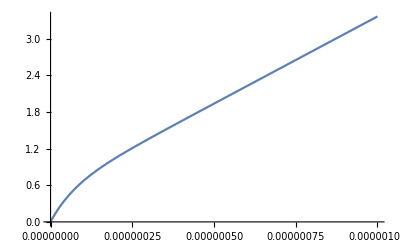

```mathematica
Plot[ezs1,{t,0,1*10^-6}]
```

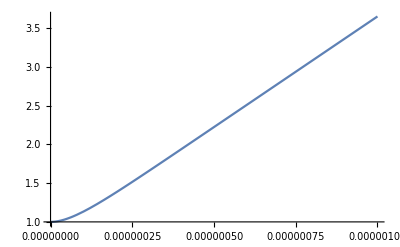

```mathematica
Plot[ezi3+ezs1,{t,0,1*10^-6}]
```